# Math 223: Homework 1

Ali Heydari

Jan 28, 2021

```mathematica
Clear["Global`*"]
```

## Problem 1

Use the Series command to compute the Taylor series of (1 + (x))^(1/x) about x = 0. Explore different parameter values to make sure you understand how to use this command. Use the Plot command to plot a comparison of this function with the polynomial of degree 4 given by the partial sum of the Taylor series over the interval [−1, 4]

Computing the first 10 Taylor series terms about the point x=0

```mathematica
n = 10
func = (1+x)^(1/x)
x0 = 0
expansion1 = Series[func,{x,x0,n}]
```

10

(1+x)^(1/x)

0

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760-(959 ⅇ x^5)/2304+(238043 ⅇ x^6)/580608-(67223 ⅇ x^7)/165888+(559440199 ⅇ x^8)/1393459200-(123377159 ⅇ x^9)/309657600+(29128857391 ⅇ x^10)/73574645760+O[x]^11

Now to play get the 4th order Taylor polynomial:

```mathematica
n = 4
```

4

```mathematica
expansion2 = Series[func,{x,x0,n}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760+O[x]^5

```mathematica
expansion2 = Normal[%]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760

Now to compare the actual function with the the Taylor polynomial of order 4:

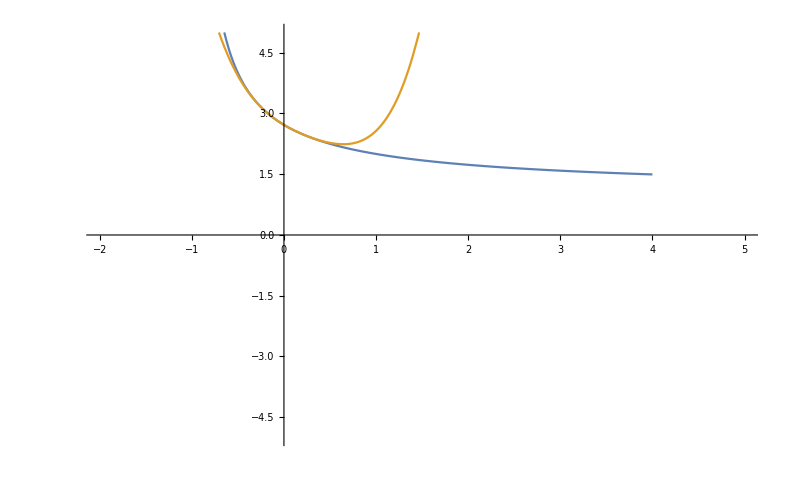

```mathematica
Plot[{func,expansion2},{x,-1,4},PlotRange->{{-2,5},{-5,5}}]
```

And the plot makes sense, since we see the expansion roughly match the function around the expanded point.

## Problem 2

Use the Integrate command to compute ∫_0^(3/2) sin(x^2) ⅆx. Then, use Series within the Integrate to integrate the polynomial of degree 6 given by the partial sums of the Taylor series of Sin(x^2) about x=0.

## Problem 3

Restate the problem here and follow up with any computations or explanations.